# BigData Optimal Tax: Life-Cycle

This notebook takes the basic life cycle model and examines what happens for many alternative combinations of capital and labor tax rates.

```mathematica
x=0; Remove["Global`*"];
```

Define the main life-cycle constants, the utility function, and the age-wage path.

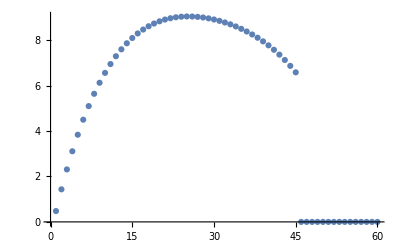

```mathematica
T=60;Tret=45;
r=0.1;R=1 + r; 
β=.95;
u[c_,l_] :=c^(1-γ)/(1-γ)-B l^(1+η)/(1+η)
Clear[w];
(* Specify age-wage path*)
Do[w[t]=-36.9994+3.52022(t+17)-.101878(t+17)^2+.00134816(t+17)^3-7.06233*10^-6(t+17)^4,{t,1,Tret}];
wagelist=Table[If[i≤ Tret,w[i],0],{i,T}];
ListPlot[wagelist]
```

We define the basic optimization problem.

```mathematica
Tax[capInc_,labInc_]:=τK (R-1) capInc   +τL labInc;
PVrevL:= Sum[τL w[t] l[t] R^(-t+1),{t,1,Tret}] ;
PVrevK:= Sum[τK (R-1) a[t] R^(-t+1),{t,1,T}] ;
PVrevC:= Sum[τC c[t] R^(-t+1),{t,1,T}] ;
```

```mathematica
obj := Sum[β^(t-1) u[c[t],l[t]],{t,1,T}];
(*Define Budget Constraints*)
bc1:=Table[(R  a[t]+w[t] l[t]-c[t]-Tax[ a[t],w[t] l[t]])-a[t+1]≥ 0,{t,1,T}];
(*Define Control variables*)
varsc:=Table[c[t],{t,1,T}];
varsl:=Table[l[t],{t,1,Tret}];
varsa:=Table[a[t],{t,2,T+1}];
vars:=Union[varsc,varsl,varsa];
(*Define bound Constraints*)
bcaT:={a[T+1]≥ 0};
abnds:=Table[a[t]≥ amin,{t,2,T}];
constraints1:=Union[bc1,bcaT,abnds];
lbndsc:=Table[c[t]≥ 0.0001,{t,1,T}];
lbndsl:=Thread[varsl≥0]; 
lbnds:=Union[lbndsc,lbndsl];
(*Collect all constraints*)
constraints:=Union[constraints1,lbnds];
```

```mathematica
(*Set initial guess for all variables to be 1; probably not a feasible point but better than letting them be zero.*)
varsinit=Table[{vars[[i]],1},{i,Length[vars]}];
```

This is the command which takes as input the tax rates, the borrowing constraints, and preference parameters, and outputs the individuals utility and taxes paid.

NOTE: This is a very simple problem. One should think of f[----] as a black box because it will often be a substantive computation on its own. In this notebook I do nothing that relies on special features of this problem. I use this problem because it is fast to compute, and it allows me to demonstrate the general concept of computing a Pareto frontier.

```mathematica
f[τK0_,τL0_,amin0_,γ0_,η0_,B0_]:=
Block[{a,c,l,utility,PVrevK0,PVrevL0,τK=τK0,τL=τL0,amin=amin0,γ=γ0,η=η0,B=B0},
(*Define border conditions particular to the problem*)
a[1]=0;
Do[ l[i]=0,{i,Tret+1,T}];
{utility,sol}=FindMaximum[{obj,constraints}, varsinit];
PVrevK0=PVrevK/.sol;PVrevL0=PVrevL/.sol;
{utility,PVrevK0+PVrevL0, PVrevK0,PVrevL0,τK,τL}
]
```

```mathematica
varsinit
```

{{a[2],1},{a[3],1},{a[4],1},{a[5],1},{a[6],1},{a[7],1},{a[8],1},{a[9],1},{a[10],1},{a[11],1},{a[12],1},{a[13],1},{a[14],1},{a[15],1},{a[16],1},{a[17],1},{a[18],1},{a[19],1},{a[20],1},{a[21],1},{a[22],1},{a[23],1},{a[24],1},{a[25],1},{a[26],1},{a[27],1},{a[28],1},{a[29],1},{a[30],1},{a[31],1},{a[32],1},{a[33],1},{a[34],1},{a[35],1},{a[36],1},{a[37],1},{a[38],1},{a[39],1},{a[40],1},{a[41],1},{a[42],1},{a[43],1},{a[44],1},{a[45],1},{a[46],1},{a[47],1},{a[48],1},{a[49],1},{a[50],1},{a[51],1},{a[52],1},{a[53],1},{a[54],1},{a[55],1},{a[56],1},{a[57],1},{a[58],1},{a[59],1},{a[60],1},{a[61],1},{c[1],1},{c[2],1},{c[3],1},{c[4],1},{c[5],1},{c[6],1},{c[7],1},{c[8],1},{c[9],1},{c[10],1},{c[11],1},{c[12],1},{c[13],1},{c[14],1},{c[15],1},{c[16],1},{c[17],1},{c[18],1},{c[19],1},{c[20],1},{c[21],1},{c[22],1},{c[23],1},{c[24],1},{c[25],1},{c[26],1},{c[27],1},{c[28],1},{c[29],1},{c[30],1},{c[31],1},{c[32],1},{c[33],1},{c[34],1},{c[35],1},{c[36],1},{c[37],1},{c[38],1},{c[39],1},{c[40],1},{c[41],1},{c[42],1},{c[43],1},{c[44],1},{c[45],1},{c[46],1},{c[47],1},{c[48],1},{c[49],1},{c[50],1},{c[51],1},{c[52],1},{c[53],1},{c[54],1},{c[55],1},{c[56],1},{c[57],1},{c[58],1},{c[59],1},{c[60],1},{l[1],1},{l[2],1},{l[3],1},{l[4],1},{l[5],1},{l[6],1},{l[7],1},{l[8],1},{l[9],1},{l[10],1},{l[11],1},{l[12],1},{l[13],1},{l[14],1},{l[15],1},{l[16],1},{l[17],1},{l[18],1},{l[19],1},{l[20],1},{l[21],1},{l[22],1},{l[23],1},{l[24],1},{l[25],1},{l[26],1},{l[27],1},{l[28],1},{l[29],1},{l[30],1},{l[31],1},{l[32],1},{l[33],1},{l[34],1},{l[35],1},{l[36],1},{l[37],1},{l[38],1},{l[39],1},{l[40],1},{l[41],1},{l[42],1},{l[43],1},{l[44],1},{l[45],1}}

Here is a simple example

```mathematica
f[.4,.5,-3000,0.5,1,1]//Timing
```

{0.125,{62.7419,39.3704,-4.45625,43.8267,0.4,0.5}}

## Create Database

Build your database (or import it if already built)

```mathematica
gamlist={1/2};
etalist={1,1.5};
```

```mathematica
tkmax=0.4; tlmax=0.4;
```

```mathematica
dtk=0.05; dtl=0.05;
```

```mathematica
ntk=tkmax/dtk+1
ntl=tlmax/dtl + 1
```

9.

9.

We next evaluate many combinations of taxes for different preferences

{tk, 0, .50, .05} ({tl, 0, .50, .05}) says that we look at tk (tl) beginning with 0 and increasing to 0.50 in steps of 0.05

{aamin,{0}} says we impose a zero lower bound on assets (meaning no borrowing allowed)

{gam,gamlist} and {eeta,etalist} means that gam is drawn from gamlist and eeta is drawn from etalist

In this version, we allow borrowing:

```mathematica
data=ParallelTable[f[tk,tl,aamin,gam,eeta,n],{tk,0,tkmax,dtk},{tl,0,tlmax,dtl},{aamin,{0}},{gam,gamlist},{eeta,etalist},{n,{1}}];//AbsoluteTiming
```

{6.52165,Null}

```mathematica
time=%[[1]];
```

tmp is the number of cases. We compute how much time is spent on each example

```mathematica
numcases=Length[gamlist] Length[etalist] ntk ntl
numcases/time
```

162.

24.8403

```mathematica
data
```

{{{{{{{116.907,0.,0.,0.,0.,0.}},{{112.597,0.,0.,0.,0.,0.}}}}},{{{{{112.977,6.1758,0.,6.1758,0.,0.05}},{{109.045,5.04673,0.,5.04673,0.,0.05}}}}},{{{{{108.977,12.131,0.,12.131,0.,0.1}},{{105.421,9.95795,0.,9.95795,0.,0.1}}}}},{{{{{104.903,17.8531,0.,17.8531,0.,0.15}},{{101.722,14.725,0.,14.725,0.,0.15}}}}},{{{{{100.747,23.3279,0.,23.3279,0.,0.2}},{{97.9395,19.338,0.,19.338,0.,0.2}}}}},{{{{{96.5047,28.5393,0.,28.5393,0.,0.25}},{{94.0675,23.7856,0.,23.7856,0.,0.25}}}}},{{{{{92.1665,33.4685,0.,33.4685,0.,0.3}},{{90.0975,28.0547,0.,28.0547,0.,0.3}}}}},{{{{{87.7236,38.0938,0.,38.0938,0.,0.35}},{{86.0196,32.1296,0.,32.1296,0.,0.35}}}}},{{{{{83.1652,42.3896,0.,42.3896,0.,0.4}},{{81.8222,35.9921,0.,35.9921,0.,0.4}}}}}},{{{{{{111.938,7.13536,7.13536,0.,0.05,0.}},{{108.2,5.70067,5.70067,0.,0.05,0.}}}}},{{{{{108.175,12.7021,6.66368,6.03841,0.05,0.05}},{{104.786,10.3108,5.34663,4.96417,0.05,0.05}}}}},{{{{{104.345,18.0613,6.2002,11.8611,0.05,0.1}},{{101.305,14.7923,4.99722,9.79504,0.05,0.1}}}}},{{{{{100.444,23.2011,5.74523,17.4559,0.05,0.15}},{{97.7494,19.1367,4.65264,14.4841,0.05,0.15}}}}},{{{{{96.4652,28.108,5.2991,22.8089,0.05,0.2}},{{94.1149,23.3347,4.31309,19.0216,0.05,0.2}}}}},{{{{{92.4028,32.7665,4.86218,27.9044,0.05,0.25}},{{90.3942,27.3753,3.9788,23.3965,0.05,0.25}}}}},{{{{{88.249,37.1588,4.43486,32.7239,0.05,0.3}},{{86.5792,31.2457,3.65005,27.5957,0.05,0.3}}}}},{{{{{83.9949,41.264,4.0176,37.2464,0.05,0.35}},{{82.6605,34.9311,3.32711,31.604,0.05,0.35}}}}},{{{{{79.6303,45.0575,3.61092,41.4466,0.05,0.4}},{{78.627,38.4136,3.01034,35.4033,0.05,0.4}}}}}},{{{{{{107.713,11.5257,11.5257,0.,0.1,0.}},{{104.452,9.27402,9.27402,0.,0.1,0.}}}}},{{{{{104.092,16.6754,10.7638,5.91156,0.1,0.05}},{{101.156,13.5857,8.69806,4.88762,0.1,0.05}}}}},{{{{{100.407,21.6272,10.0152,11.612,0.1,0.1}},{{97.7951,17.7736,8.12964,9.64401,0.1,0.1}}}}},{{{{{96.6525,26.3695,9.2803,17.0892,0.1,0.15}},{{94.3631,21.8298,7.56905,14.2608,0.1,0.15}}}}},{{{{{92.8241,30.8895,8.5597,22.3298,0.1,0.2}},{{90.8546,25.745,7.01666,18.7283,0.1,0.2}}}}},{{{{{88.9149,35.1721,7.85391,27.3182,0.1,0.25}},{{87.2627,29.5086,6.47284,23.0357,0.1,0.25}}}}},{{{{{84.9179,39.2001,7.16363,32.0365,0.1,0.3}},{{83.5799,33.1082,5.938,27.1702,0.1,0.3}}}}},{{{{{80.8245,42.9536,6.48968,36.464,0.1,0.35}},{{79.797,36.5293,5.41265,31.1167,0.1,0.35}}}}},{{{{{76.6246,46.4086,5.83272,40.5759,0.1,0.4}},{{75.9032,39.7547,4.8973,34.8574,0.1,0.4}}}}}},{{{{{{104.156,13.841,13.841,0.,0.15,0.}},{{101.295,11.1447,11.1447,0.,0.15,0.}}}}},{{{{{100.654,18.721,12.9261,5.79496,0.15,0.05}},{{98.0987,15.2692,10.4525,4.8167,0.15,0.05}}}}},{{{{{97.0908,23.41,12.027,11.3829,0.15,0.1}},{{94.8391,19.2735,9.76945,9.50407,0.15,0.1}}}}},{{{{{93.4607,27.8966,11.1445,16.7521,0.15,0.15}},{{91.5109,23.1496,9.09579,14.0538,0.15,0.15}}}}},{{{{{89.7587,32.1684,10.2791,21.8893,0.15,0.2}},{{88.1084,26.8886,8.43198,18.4566,0.15,0.2}}}}},{{{{{85.9786,36.2109,9.43156,26.7793,0.15,0.25}},{{84.6251,30.48,7.77846,22.7015,0.15,0.25}}}}},{{{{{82.1136,40.0073,8.60266,31.4046,0.15,0.3}},{{81.0536,33.9117,7.13575,26.776,0.15,0.3}}}}},{{{{{78.1553,43.538,7.79327,35.7447,0.15,0.35}},{{77.385,37.1696,6.50442,30.6652,0.15,0.35}}}}},{{{{{74.0941,46.78,7.00439,39.7756,0.15,0.4}},{{73.6089,40.2367,5.88513,34.3516,0.15,0.4}}}}}},{{{{{{101.201,14.4931,14.4931,0.,0.2,0.}},{{98.6679,11.6842,11.6842,0.,0.2,0.}}}}},{{{{{97.7989,19.2224,13.535,5.68741,0.2,0.05}},{{95.5549,15.7096,10.9586,4.75102,0.2,0.05}}}}},{{{{{94.3365,23.7653,12.5936,11.1717,0.2,0.1}},{{92.3799,19.6169,10.2424,9.37446,0.2,0.1}}}}},{{{{{90.8094,28.1107,11.6695,16.4412,0.2,0.15}},{{89.138,23.3983,9.53614,13.8622,0.2,0.15}}}}},{{{{{87.2124,32.2464,10.7633,21.4831,0.2,0.2}},{{85.8237,27.0451,8.84022,18.2049,0.2,0.2}}}}},{{{{{83.5396,36.1582,9.87586,26.2823,0.2,0.25}},{{82.4307,30.5469,8.15503,22.3919,0.2,0.25}}}}},{{{{{79.7842,39.8297,9.00791,30.8217,0.2,0.3}},{{78.9518,33.892,7.48121,26.4108,0.2,0.3}}}}},{{{{{75.9382,43.2417,8.1604,35.0813,0.2,0.35}},{{75.3784,37.0663,6.81932,30.247,0.2,0.35}}}}},{{{{{71.9922,46.3717,7.33435,39.0374,0.2,0.4}},{{71.7002,40.0532,6.17005,33.8831,0.2,0.4}}}}}},{{{{{{98.7856,13.8887,13.8887,0.,0.25,0.}},{{96.5207,11.2276,11.2276,0.,0.25,0.}}}}},{{{{{95.4647,18.5593,12.9706,5.58864,0.25,0.05}},{{93.4755,15.2211,10.5303,4.69081,0.25,0.05}}}}},{{{{{92.085,23.0461,12.0685,10.9776,0.25,0.1}},{{90.3696,19.0978,9.84212,9.25567,0.25,0.1}}}}},{{{{{88.642,27.3386,11.1829,16.1557,0.25,0.15}},{{87.1982,22.85,9.16348,13.6865,0.25,0.15}}}}},{{{{{85.1309,31.4245,10.3145,21.11,0.25,0.2}},{{83.956,26.4689,8.49473,17.9742,0.25,0.2}}}}},{{{{{81.5457,35.29,9.46407,25.8259,0.25,0.25}},{{80.6369,29.9445,7.83633,22.1082,0.25,0.25}}}}},{{{{{77.88,38.9188,8.63231,30.2865,0.25,0.3}},{{77.2337,33.265,7.18883,26.0761,0.25,0.3}}}}},{{{{{74.1258,42.2922,7.82013,34.4721,0.25,0.35}},{{73.738,36.4165,6.55282,29.8637,0.25,0.35}}}}},{{{{{70.274,45.3879,7.02853,38.3594,0.25,0.4}},{{70.1399,39.3827,5.92892,33.4538,0.25,0.4}}}}}},{{{{{{96.8517,12.3835,12.3835,0.,0.3,0.}},{{94.8016,10.0077,10.0077,0.,0.3,0.}}}}},{{{{{93.5958,17.0639,11.5649,5.49895,0.3,0.05}},{{91.8106,14.0224,9.38656,4.63587,0.3,0.05}}}}},{{{{{90.2822,21.562,10.7605,10.8015,0.3,0.1}},{{88.76,17.9201,8.77286,9.14725,0.3,0.1}}}}},{{{{{86.9067,25.8674,9.97094,15.8964,0.3,0.15}},{{85.6451,21.6941,8.16793,13.5262,0.3,0.15}}}}},{{{{{83.4642,29.9679,9.19668,20.7712,0.3,0.2}},{{82.4607,25.3354,7.57171,17.7637,0.3,0.2}}}}},{{{{{79.9493,33.8498,8.43838,25.4114,0.3,0.25}},{{79.2007,28.8344,6.98524,21.8492,0.3,0.25}}}}},{{{{{76.3553,37.4972,7.69677,29.8004,0.3,0.3}},{{75.8581,32.1788,6.40814,25.7707,0.3,0.3}}}}},{{{{{72.6746,40.8915,6.97261,33.9188,0.3,0.35}},{{72.4247,35.3548,5.84087,29.5139,0.3,0.35}}}}},{{{{{68.8982,44.0106,6.2668,37.7438,0.3,0.4}},{{68.8906,38.3466,5.28475,33.0619,0.3,0.4}}}}}},{{{{{{95.3422,10.2728,10.2728,0.,0.35,0.}},{{93.4595,8.34773,8.34773,0.,0.35,0.}}}}},{{{{{92.1371,15.0124,9.59375,5.41865,0.35,0.05}},{{90.5108,12.4165,7.82929,4.58721,0.35,0.05}}}}},{{{{{88.8751,19.5702,8.92648,10.6437,0.35,0.1}},{{87.5034,16.3689,7.31764,9.05124,0.35,0.1}}}}},{{{{{85.5522,23.9358,8.27148,15.6643,0.35,0.15}},{{84.4326,20.1973,6.81306,13.3842,0.35,0.15}}}}},{{{{{82.1634,28.0971,7.62919,20.4679,0.35,0.2}},{{81.2933,23.8931,6.31583,17.5772,0.35,0.2}}}}},{{{{{78.7033,32.0404,7.00006,25.0403,0.35,0.25}},{{78.0794,27.4462,5.82633,21.6199,0.35,0.25}}}}},{{{{{75.1653,35.7502,6.38496,29.3653,0.35,0.3}},{{74.7842,30.8451,5.34492,25.5002,0.35,0.3}}}}},{{{{{71.542,39.2079,5.78431,33.4236,0.35,0.35}},{{71.3993,34.0762,4.87204,29.2041,0.35,0.35}}}}},{{{{{67.8244,42.3914,5.19874,37.1926,0.35,0.4}},{{67.9153,37.1231,4.40816,32.7149,0.35,0.4}}}}}},{{{{{{94.1987,7.95711,7.95711,0.,0.4,0.}},{{92.4423,6.46292,6.46292,0.,0.4,0.}}}}},{{{{{91.032,12.7811,7.43114,5.34999,0.4,0.05}},{{89.5257,10.6067,6.06155,4.54515,0.4,0.05}}}}},{{{{{87.8092,17.4232,6.91429,10.5089,0.4,0.1}},{{86.551,14.6337,5.66542,8.96825,0.4,0.1}}}}},{{{{{84.5261,21.8727,6.40693,15.4658,0.4,0.15}},{{83.5136,18.5363,5.27476,13.2615,0.4,0.15}}}}},{{{{{81.178,26.118,5.90942,20.2085,0.4,0.2}},{{80.4085,22.3059,4.8898,17.4161,0.4,0.2}}}}},{{{{{77.7593,30.1452,5.42216,24.7231,0.4,0.25}},{{77.2296,25.9325,4.51082,21.4216,0.4,0.25}}}}},{{{{{74.2638,33.9388,4.94563,28.9932,0.4,0.3}},{{73.9702,29.4045,4.13811,25.2664,0.4,0.3}}}}},{{{{{70.6839,37.4803,4.48032,33.,0.4,0.35}},{{70.6222,32.7083,3.77199,28.9363,0.4,0.35}}}}},{{{{{67.0109,40.7482,4.02679,36.7214,0.4,0.4}},{{67.1761,35.8278,3.41286,32.4149,0.4,0.4}}}}}}}

output data

```mathematica
data>> dataoutMay2;
```

Next, we read the file

```mathematica
Clear[data]
data=<<dataoutMay2;
```

## The Pareto frontier - tables

In this notebook we care about utility versus revenue. I look forward to higher-dimensional frontiers.

Define Pareto function and Pareto frontier

Function h receives:
	Data in from database of cases
	Target revenue
	Indices - γind and ηind - indicating preference parameters

Function h outputs the optimal element for that revenue, and the policies that produced that outcome.

```mathematica
h[data_,revenue_, alimind_,γind_,ηind_]:=Module[
{dataflat,util,comb},
dataflat=Flatten[data[[All,All,alimind,γind,ηind,1]],1];
util=Max[Select[dataflat,#[[2]]≥revenue&][[All,1]]];
comb=Select[dataflat,#[[1]]==util&]
]
```

```mathematica
casesprefs=Table[{gamlist[[gam]],etalist[[eeta]]},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
casesprefs=Flatten[casesprefs,1];
```

```mathematica
cases=Table[{1,gam,eeta},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
cases=Flatten[cases,1];
```

```mathematica
numcases=Length[cases];
count=0;
```

```mathematica
outcmd:= (count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
tb=Table[h[data,rev,i,j,k][[1]],{rev,0,0.99 maxrev ,0.04 maxrev}];
TableForm[tb,TableHeadings->{{},{"util","revtot","revk","revl","tk","tl"}}])
```

```mathematica
outcmdold:= (
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
Table[h[data,rev,i,j,k][[1]],{rev,0,0.96 maxrev ,0.02 maxrev}]//TableForm)
```

```mathematica
outcmd
```

gamma = 1/2,   eta = 1

| util | revtot | revk | revl | tk | tl
 | 116.907 | 0. | 0. | 0. | 0. | 0.
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 112.977 | 6.1758 | 0. | 6.1758 | 0. | 0.05
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 108.977 | 12.131 | 0. | 12.131 | 0. | 0.1
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 104.903 | 17.8531 | 0. | 17.8531 | 0. | 0.15
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 100.747 | 23.3279 | 0. | 23.3279 | 0. | 0.2
 | 96.6525 | 26.3695 | 9.2803 | 17.0892 | 0.1 | 0.15
 | 96.6525 | 26.3695 | 9.2803 | 17.0892 | 0.1 | 0.15
 | 96.5047 | 28.5393 | 0. | 28.5393 | 0. | 0.25
 | 92.8241 | 30.8895 | 8.5597 | 22.3298 | 0.1 | 0.2
 | 92.4028 | 32.7665 | 4.86218 | 27.9044 | 0.05 | 0.25
 | 88.9149 | 35.1721 | 7.85391 | 27.3182 | 0.1 | 0.25
 | 88.249 | 37.1588 | 4.43486 | 32.7239 | 0.05 | 0.3
 | 87.7236 | 38.0938 | 0. | 38.0938 | 0. | 0.35
 | 83.9949 | 41.264 | 4.0176 | 37.2464 | 0.05 | 0.35
 | 83.9949 | 41.264 | 4.0176 | 37.2464 | 0.05 | 0.35
 | 79.6303 | 45.0575 | 3.61092 | 41.4466 | 0.05 | 0.4
 | 79.6303 | 45.0575 | 3.61092 | 41.4466 | 0.05 | 0.4

## The Pareto frontier - graphs

### Plot all data

We plot all the data points in revenue-utility space. This helps us see where the good points are. I also use colors to indicate the policies.

plot

```mathematica
tmax=Max[tkmax,tlmax]
```

0.4

```mathematica
plot[alimind_,γind_,ηind_]:=Module[

{alimi=alimind,γi=γind,ηi=ηind,Βi=1,dots,colorF,gra1,gra2,plotLegend,leg},

dots=Flatten[data[[All,All,alimi,γi,ηi,Βi]],1];

colorF=Blend[{{0,Green},{tmax,Red}},#]&;

gra1=Graphics[
{{colorF[#5],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τK",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},
Frame->{{True,False},{True,False}}, 
PlotRange->All,
AxesOrigin->{0,0},
FrameLabel-> {"Total Tax Revenue","Consumer Utility"},
ImageSize->Medium,
AxesOrigin-> {0,0}];

gra2=Graphics[{{colorF[#6],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τL",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},Frame->{{True,False},{True,False}}, PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"Total Tax Revenue","Consumer Utility"},ImageSize->Medium,AxesOrigin-> {0,0}];

plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->True,FrameTicks->None,PlotRangePadding->.5];

leg=plotLegend[{0,0.8},20,colorF];
Grid[{{Row[{"γ= ",2^(γi-2), ", η= ",Piecewise[{{10,ηi==4},{5,ηi==3}},ηi ] , ", Borrowinglimit= ",Piecewise[{{-(alimi-1)*10,alimi<4},{-50,alimi==4}},-∞]}],SpanFromLeft},{gra1,gra2,leg}},ItemSize->Automatic]
]
```

```mathematica
count=0;
```

```mathematica
prntcmd:=(
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]];
plot[i,j,k])
```

Each plot is a point in utility-revenue space. The left one uses color to indicate the size of the capital income tax; the right one does so for the labor income tax.
Note that there are some red points in the τL graph that are on the frontier, but the red points in the τK graph are all inferior.

gamma = 1/2,   eta = 1

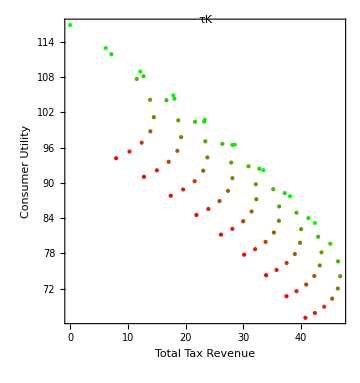
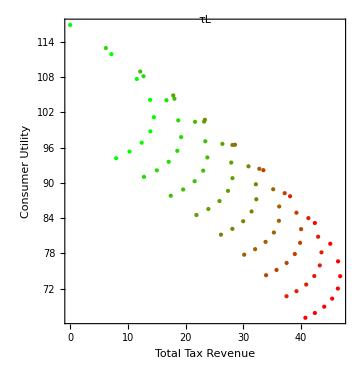
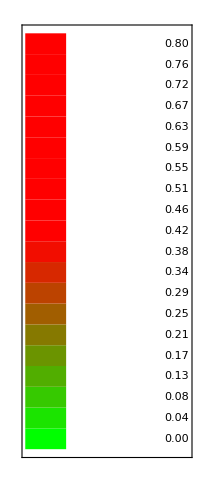
γ= 1/2, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```